```mathematica
data={{0,1},{2,3},{4,0},{6,-2},{8,1},{10,4}};
```

```mathematica
interpFunc=Interpolation[data,Method->"Spline"];
```

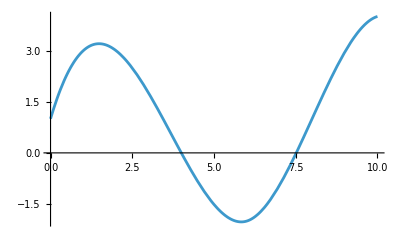

```mathematica
Plot[interpFunc[x],{x,0,10}]
```

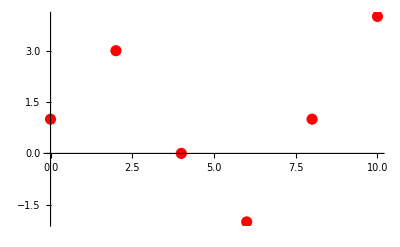

```mathematica
redDotPoint=ListPlot[data,PlotStyle->{Red,PointSize[0.02]}]
```

```mathematica
greenPoint[t_]:=Graphics[{Green,PointSize[0.03],Point[{t,interpFunc[t]}]}]
```

```mathematica
Manipulate[Show[Plot[interpFunc[x],{x,0,t},PlotStyle->{Blue,Thick},PlotRange->{{-1,11},{-3,5}}],redDotPoint,greenPoint[t]],{t,0.0001,10.000-0.0001,0.1}]
```